```mathematica
(*F = ma sprendinys*)
Clear[F,m,c]
(*Solve the differential equation*)
sol1=DSolve[{z''[t]==F/m*Sqrt[(1-(t*z''[t]/c)^2)],z[0]==0,z'[0]==0},z[t],t]
sol1a = DSolve[{z''[t]==F/m*Sqrt[(1-(z'[t]/c)^2)],z[0]==0,z'[0]==0},z[t],t]
D[D[sol1[[2]],t],t]
```

{{z[t]→-(c (√(c^2 m^2)-√(c^2 m^2+F^2 t^2)+F t ArcTanh[(F t)/(√(c^2 m^2+F^2 t^2))]))/F},{z[t]→(c (√(c^2 m^2)-√(c^2 m^2+F^2 t^2)+F t ArcTanh[(F t)/(√(c^2 m^2+F^2 t^2))]))/F}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z[t]→(-c^2 m+c^2 m Cos[(F t)/(c m)])/F},{z[t]→(c^2 m+c^2 m Cos[(-c m π+F t)/(c m)])/F}}

{z''[t]→(c ((F^4 t^2)/((c^2 m^2+F^2 t^2)^(3/2))-F^2/(√(c^2 m^2+F^2 t^2))+(F t ((3 F^5 t^3)/((c^2 m^2+F^2 t^2)^(5/2))-(3 F^3 t)/((c^2 m^2+F^2 t^2)^(3/2))))/(1-(F^2 t^2)/(c^2 m^2+F^2 t^2))-(F t ((2 F^4 t^3)/((c^2 m^2+F^2 t^2)^2)-(2 F^2 t)/(c^2 m^2+F^2 t^2)) (-(F^3 t^2)/((c^2 m^2+F^2 t^2)^(3/2))+F/(√(c^2 m^2+F^2 t^2))))/((1-(F^2 t^2)/(c^2 m^2+F^2 t^2))^2)+(2 F (-(F^3 t^2)/((c^2 m^2+F^2 t^2)^(3/2))+F/(√(c^2 m^2+F^2 t^2))))/(1-(F^2 t^2)/(c^2 m^2+F^2 t^2))))/F}

```mathematica
(*Define the parameters*)
(*F=10; (*Force*)*)
m=0.005; (*Mass*)
c=3*10^8; (*Speed of light*)
```

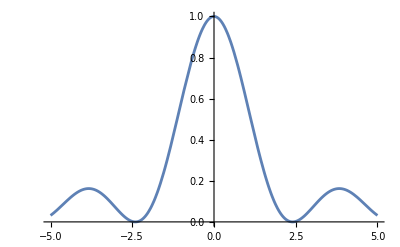

```mathematica
Plot[Abs[BesselJ[0,x]]^2,{x,-5,5}]
```

```mathematica
(*Duoda atstumą iki pirmo nulio*)
N[BesselJZero[0,1]]
```

2.40483

```mathematica
(* Burės paviršiaus plotas () *)
Sail=2*Pi*Integrate[x,{x,0,N[BesselJZero[0,1]]}]
```

18.1684

```mathematica
(*Intensyvumo funkcija paveikta x operatoriumi ir suintegruota.
Gaunasi vidutinė intensyvumo reikšmė per visą paviršių*)
Beselis=2*Pi*Integrate[x*Abs[BesselJ[0,x]]^2,{x,0,N[BesselJZero[0,1]]}]
```

4.89664

```mathematica
Clear[F]
P = 1000000; (*Beam overall power*)
(*Force acting on sail*)
F = 4*Pi*P/c*Integrate[x*Abs[BesselJ[0,x]]^2, {x, 0, N[BesselJZero[0,1]]}]
```

0.0326443

```mathematica
(*Extract the solution function*)
zSol[t_]=z[t]/. sol1[[2]];
(*Plot the solution*)
Manipulate[Plot[zSol[t],{t,0,tMax},PlotRange->{{0,tMax},Automatic},AxesLabel->{"t","z(t)"},PlotLabel->"Solution to the Differential Equation",GridLines->Automatic],
{{tMax,10,"Maximum Time"},1,1000,1}
]
```

```mathematica
(*Define the parameters*)
Clear[P,F,m,c];
m= 0.01; (*mass*)
c=3*10^8; (*speed of light*)
w0=1; (*waist radius*)
n=1; (*refraction index*)
lam=600*10^-9; (*wavelength*)
(*Bessel beam overall power*)
gRadius[z_]:=w0*Sqrt[1+(z^2)/Zr^2]; (*Gauss radius*)
Zr=N[Pi]*w0^2*n/lam; (*Rayleigh range*)
radius = 1;

(*Bessel part*)
I0[P_] := 2*P/N[Pi]/w0^2; (*Beam overall power*)
(*Force acting on sail*)
F[P_] := P/c*Integrate[x*Abs[BesselJ[0,x]]^2, {x, 0, w0}];
Powa[Pow_] := Pow/c*Integrate[x*Abs[BesselJ[0,x]]^2, {x, 0, w0}];

(*Define the ODE with the new gIntensity[z[t]]*)
gIntensity[z_,P_]:=I0[P]/c*(w0/gRadius[z])^2*Exp[-2*r^2/gRadius[z]^2];
eqn[P_]:=z''[t]*m/Sqrt[(1-(t*z''[t]/c)^2)]==Integrate[gIntensity[z[t], P],{r,0,w0}];

(*Define the initial conditions*)
initialConditions={z'[0]==0,z[0]==0};
(*Solve the ODE numerically*)
Tmax=1000; (*You can adjust this based on your problem*)
PValues = {1*^8, 1*^9, 1*^10};
sol2[P_?NumericQ] :=NDSolve[{eqn[P],initialConditions},z,{t,0,Tmax}];
Clear[P];
(*čia piešiasi Gausas, silpsta stipriai pagreitis didejant atstumui*)
FValues= Table[Powa[P], {P, PValues}];
table1 = Table[
z[t]/. sol2[P][[2]],
{P, PValues}
];

table2 = Table[
Derivative[1][z][t]/. sol2[P][[2]],
{P, PValues}
];
table3 = Table[
Derivative[2][z][t]/. sol2[P][[2]],
{P, PValues}
];
(*F = Powa[P];
Evaluate[z[t]/. sol1[[2]]];
F = Powa[2];
Evaluate[z[t]/. sol1[[2]]];*)

(*Čia piešiasi Besselis, silpsta pagreitis del releatyvistiniu efektu (silpnai)*)
table4=Table[
z[t]/. sol1[[2]],
{F, FValues}
];
table5=Table[
D[z[t]/.sol1[[2]],t],
{F, FValues}
];
table6=Table[
D[D[z[t]/.sol1[[2]],t],t],
{F, FValues}
];
{z->InterpolatingFunction[…]}
```

{100000000 W,1000000000 W,10000000000 W}

{z→InterpolatingFunction[…]}

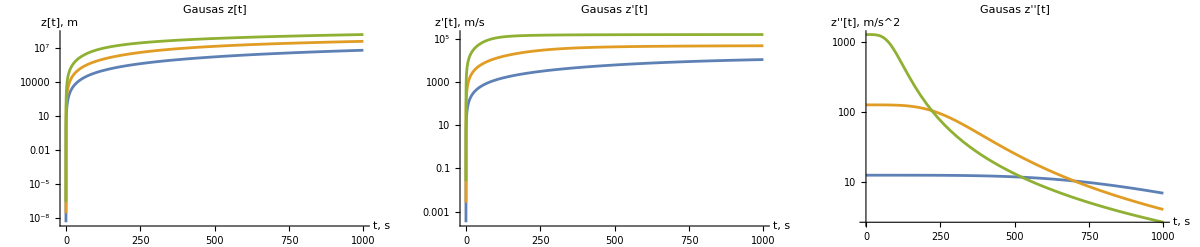

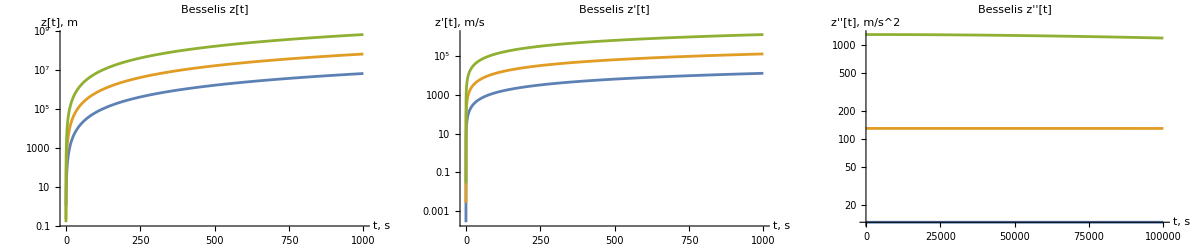

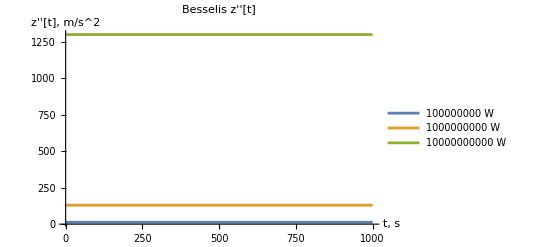
show[-Graphics-]

```mathematica
plot1=LogPlot[Evaluate[table1],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z[t], m"},PlotLabel->"Gausas z[t]"];

plot2=LogPlot[Evaluate[table2],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z'[t], m/s"},PlotLabel->"Gausas z'[t]"];

plot3=LogPlot[Evaluate[table3],{t,0.0001,Tmax},PlotRange->All,AxesLabel->{"t, s","z''[t], m/s^2"},PlotLabel->"Gausas z''[t]"];

plot4=LogPlot[Evaluate[table4],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z[t], m"},PlotLabel->"Besselis z[t]"];

plot5=LogPlot[Evaluate[table5],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z'[t], m/s"},PlotLabel->"Besselis z'[t]"];

plot6=LogPlot[Evaluate[table6],{t,0,Tmax*100},PlotRange->All,AxesLabel->{"t, s","z''[t], m/s^2"},PlotLabel->"Besselis z''[t]"];


GraphicsGrid[{{plot1,plot2,plot3}},Spacings->{0,0},ImageSize->Full]
GraphicsGrid[{{plot4,plot5,plot6}},Spacings->{0,0},ImageSize->Full]

plot6=Plot[Evaluate[table6],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z''[t], m/s^2"},PlotLabel->"Besselis z''[t]",PlotLegends->PValues"W"];
show[plot6]
```